```mathematica
Quit[];
```

```mathematica
<<Lhe`
<<Lorentz`
```

```mathematica
Analysis1[eventlist_,Nev_]:=Module[{worklist,Npart,qlist,q2list,partlist,p1,p2,Ee,q2},
Npart=4;
partlist=Range[Npart];
qlist={};
q2list={};
Do[worklist=eventlist[[ievent]];
partlist=FourVectorFrom/@worklist;
p1=partlist[[1]];
p2=partlist[[3]];
Ee=partlist[[4,1]];
If[24>Ee>3,
q2=FS[p2-p1];
q2list=AppendTo[q2list,q2];
qlist=AppendTo[qlist,√-q2];
]
,{ievent,1,Nev}];
Return[qlist]]
```

```mathematica
dir="/Users/yoshi/projects/LmLt/";
lhe=dir<>"Events/run_10_0.01/unweighted_events.lhe";
lheE10M10=LoadLhe[lhe];
```

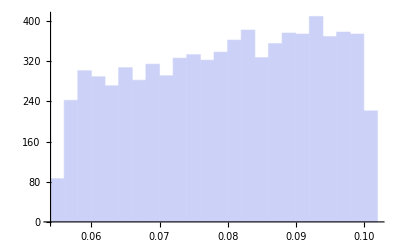

```mathematica
qE10M10=Analysis1[lheE10M10,10000];
Histogram[qE10M10]
```